```mathematica
Solve[{n1==A+B/λ1^2,n2==A+B/λ2^2},{A,B}]//Simplify
```

{{A→(n1 λ1^2-n2 λ2^2)/(λ1^2-λ2^2),B→((-n1+n2) λ1^2 λ2^2)/(λ1^2-λ2^2)}}

```mathematica
f[λ_]=(n1λ1^2-n2λ2^2)/(λ1^2-λ2^2)+1/λ^2((-n1+n2)λ1^2 λ2^2)/(λ1^2-λ2^2)
```

(n1λ1^2-n2λ2^2)/(λ1^2-λ2^2)+((-n1+n2) λ1^2 λ2^2)/(λ^2 (λ1^2-λ2^2))

```mathematica
Flatten@Solve[(n2-1)==(1-ϵ)(n1-1),n2]
fϵ[λ_]=Collect[f[λ]/.%,{ϵ},FullSimplify]
```

{n2→n1+ϵ-n1 ϵ}

(n1λ1^2-n2λ2^2)/(λ1^2-λ2^2)-((-1+n1) ϵ λ1^2 λ2^2)/(λ^2 (λ1^2-λ2^2))

```mathematica
refrIndxCauchy[n400_:1.6,λ_:551,ϵ_:0.2]=Module[{λ1=400,n1=n400,λ2=720},{n1+((-1+n1)ϵ(λ^2-λ1^2)λ2^2)/(λ^2(λ1^2-λ2^2)),ColorData["VisibleSpectrum"][λ]}];
```

```mathematica
refrIndxCauchy[1.6,#,0.15]&/@Table[x,{x,400,720,20}]//TableForm
```

1.6 | RGBColor[0.2633466723690612, 0., 0.6327450935625103]
1.5879 | RGBColor[0.4377255008513744, 0., 1.]
1.57741 | RGBColor[0.3776293607913085, 0., 1.]
1.56826 | RGBColor[0.06169090683532, 0.08573096570177553, 1.]
1.56022 | RGBColor[0., 0.44148698824292576, 0.7932403760642176]
1.55314 | RGBColor[0., 0.6711907910484065, 0.4917645794210658]
1.54685 | RGBColor[0., 0.901529955728533, 0.15903413605773167]
1.54125 | RGBColor[0., 0.9994915222573584, 0.]
1.53624 | RGBColor[0., 1., 0.]
1.53174 | RGBColor[0.6466439931895577, 0.9680892094211122, 0.]
1.52768 | RGBColor[0.9811607881294089, 0.7938591772480338, 0.]
1.52401 | RGBColor[1., 0.4974129911626398, 0.]
1.52067 | RGBColor[1., 0., 0.]
1.51764 | RGBColor[1., 0., 0.]
1.51487 | RGBColor[0.8938920360820561, 0., 0.]
1.51233 | RGBColor[0.6198256773958168, 0., 0.]
1.51 | RGBColor[0.3901335575285817, 0., 0.]

```mathematica
cauchyAB[id_]:=Module[{AB},
AB={{"Fused silica",{1.4580,0.00354}},{"Borosilicate glass BK7",{1.5046,0.00420}},{"Hard crown glass K5",{1.5220,0.00459}},{"Barium crown glass BaK4",{1.5690,0.00531}},{"Barium flint glass BaF10",{1.6700,0.00743}},{"Dense flint glass SF10",{1.7280,0.01342}}};
AB[[id,2]]]
```

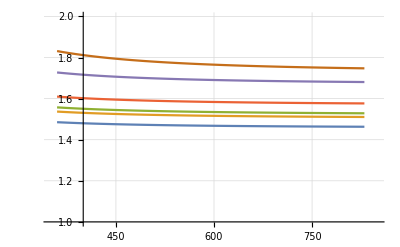

```mathematica
disf=(#[[1]]+1/(λ/1000)^2#[[2]])&/@Array[cauchyAB,6];
Plot[disf,{λ,360,830},PlotRange->{{350,850},{1,2}},GridLines->Automatic]
```

```mathematica
idx=6;
disfFitA[λ_]=Fit[disf[idx],{1,1/λ^2},λ]
NonlinearModelFit[disf[idx],A+B/λ^2,{A,B},λ]["ParameterTable"]
disfFitB[λ_]=Fit[disf[idx],{1,1/λ^2,1/λ},λ]
NonlinearModelFit[disf[idx],A+C/λ+B/λ^2,{A,B,C},λ]["ParameterTable"]
gA=Plot[disfFitA[λ],{λ,400,1100},PlotStyle->Red];
gB=Plot[disfFitB[λ],{λ,400,1100},PlotStyle->Black];
gBog=ListPlot[#,Joined->False]&@disf[idx];
Show[{gBog,gB,gA},Frame->True,FrameLabel->{"λ [nm]","n"},PlotRange->{{400,1100},Automatic}]
```

Fit::fitd: First argument {1.458  + 3540./λ^2, 1.5046  + 4200./λ^2, 1.522  + 4590./λ^2, 1.569  + 5310./λ^2, 1.67  + 7430./λ^2, 1.728  + 13420./λ^2}[6] in Fit is not a list or a rectangular array.

Fit[{1.458+3540./λ^2,1.5046+4200./λ^2,1.522+4590./λ^2,1.569+5310./λ^2,1.67+7430./λ^2,1.728+13420./λ^2}[6],{1,1/λ^2},λ]

NonlinearModelFit::fitd: First argument {1.458  + 3540./λ^2, 1.5046  + 4200./λ^2, 1.522  + 4590./λ^2, 1.569  + 5310./λ^2, 1.67  + 7430./λ^2, 1.728  + 13420./λ^2}[6] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[{1.458+3540./λ^2,1.5046+4200./λ^2,1.522+4590./λ^2,1.569+5310./λ^2,1.67+7430./λ^2,1.728+13420./λ^2}[6],A+B/λ^2,{A,B},λ][ParameterTable]

Fit::fitd: First argument {1.458  + 3540./λ^2, 1.5046  + 4200./λ^2, 1.522  + 4590./λ^2, 1.569  + 5310./λ^2, 1.67  + 7430./λ^2, 1.728  + 13420./λ^2}[6] in Fit is not a list or a rectangular array.

Fit[{1.458+3540./λ^2,1.5046+4200./λ^2,1.522+4590./λ^2,1.569+5310./λ^2,1.67+7430./λ^2,1.728+13420./λ^2}[6],{1,1/λ^2,1/λ},λ]

NonlinearModelFit::fitd: First argument {1.458  + 3540./λ^2, 1.5046  + 4200./λ^2, 1.522  + 4590./λ^2, 1.569  + 5310./λ^2, 1.67  + 7430./λ^2, 1.728  + 13420./λ^2}[6] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[{1.458+3540./λ^2,1.5046+4200./λ^2,1.522+4590./λ^2,1.569+5310./λ^2,1.67+7430./λ^2,1.728+13420./λ^2}[6],A+B/λ^2+C/λ,{A,B,C},λ][ParameterTable]

General::ivar: 400.014 is not a valid variable.

General::ivar: 414.3 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

General::ivar: 400.014 is not a valid variable.

General::ivar: 414.3 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ListPlot::lpn: {1.458  + 3540./λ^2, 1.5046  + 4200./λ^2, 1.522  + 4590./λ^2, 1.569  + 5310./λ^2, 1.67  + 7430./λ^2, 1.728  + 13420./λ^2}[6.] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in {ListPlot[{1.458`  + 3540.`/λ^2, 1.5046`  + 4200.`/λ^2, 1.522`  + 4590.`/λ^2, 1.569`  + 5310.`/λ^2, 1.67`  + 7430.`/λ^2, 1.728`  + 13420.`/λ^2}[6], Joined → False], GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[400.`, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Show[{ListPlot[{1.458+3540./λ^2,1.5046+4200./λ^2,1.522+4590./λ^2,1.569+5310./λ^2,1.67+7430./λ^2,1.728+13420./λ^2}[6],Joined→False],-Graphics-,-Graphics-},Frame→True,FrameLabel→{λ [nm],n},PlotRange→{{400,1100},Automatic}]